# Calculation of eikonal corrections at KE = 100 MeV

9/19/13

## Define Constants

```mathematica
mp=0.938272046;(*GeV/c^2*)
mn=1.00137842*mp(*GeV/c^2*);
M=2*mp+2*mn;
m=M/4;
ℏc=0.19732697178(*Giga ElectronVolt*Femto Meter*);
r=.535^(-1/2)(*Femto Meter*);
B=1/4*r^2/ℏc^2(*(c/GeV)^2*);
A=4;
```

```mathematica
En=.100(*GeV*);
EnL=En+mp;
s=mp^2+M^2+2*M*EnL;
ϵ=EnL/(M/Sqrt[s]);
P=Sqrt[EnL^2-mp^2];
k=P*(M/Sqrt[s]);
s2=mp^2+m^2+2*m*EnL;
ϵ2=EnL*(m/Sqrt[s2]);
κ=P*(m/Sqrt[s2]);
ηO=(1-ϵ/M)*(mp+M)/Sqrt[s];
ηD=(1-ϵ/ϵ2+(A-1)*ϵ/M)*(mp+M)/Sqrt[s];
```

## Import data and convert it from degrees and mbarn^1/2 to momentum transfer and fm

```mathematica
pp100a=Import["/Users/Micah/Documents/JerryDuty/eikexp/pp100a.csv"];
pp100b=Import["/Users/Micah/Documents/JerryDuty/eikexp/pp100b.csv"];
```

```mathematica
(*pp100a=Import["/phys/users/mbuuck/JerryDuty/eikexp/pp100a.csv"];
pp100b=Import["/phys/users/mbuuck/JerryDuty/eikexp/pp100b.csv"];*)
```

```mathematica
pp100a=Transpose[{pp100a[[All,1]],pp100a[[All,2]]+I*pp100a[[All,3]]}];
pp100b=Transpose[{pp100b[[All,1]],pp100b[[All,2]]+I*pp100b[[All,3]]}];
```

```mathematica
θpp100=Transpose[{pp100a[[All,1]],(pp100a[[All,2]]+pp100b[[All,2]])/2}];
```

```mathematica
θtoq[x_]:={2 κ Sin[x[[1]] Pi/360],x[[2]]/Sqrt[10]}
```

```mathematica
pp100=θtoq/@θpp100;
```

```mathematica
pn100a=Import["/Users/Micah/Documents/JerryDuty/eikexp/pn100a.csv"];
pn100b=Import["/Users/Micah/Documents/JerryDuty/eikexp/pn100b.csv"];
```

```mathematica
(*pn100a=Import["/phys/users/mbuuck/JerryDuty/eikexp/pn100a.csv"];
pn100b=Import["/phys/users/mbuuck/JerryDuty/eikexp/pn100b.csv"];*)
```

```mathematica
pn100a=Transpose[{pn100a[[All,1]],pn100a[[All,2]]+I*pn100a[[All,3]]}];
pn100b=Transpose[{pn100b[[All,1]],pn100b[[All,2]]+I*pn100b[[All,3]]}];
```

```mathematica
θpn100=Transpose[{pn100a[[All,1]],(pn100a[[All,2]]+pn100b[[All,2]])/2}];
```

```mathematica
pn100=θtoq/@θpn100;
```

```mathematica
NN100=(pp100+pn100)/2;
f=Interpolation[NN100];
fp=Interpolation[pp100];
fn=Interpolation[pn100];
```

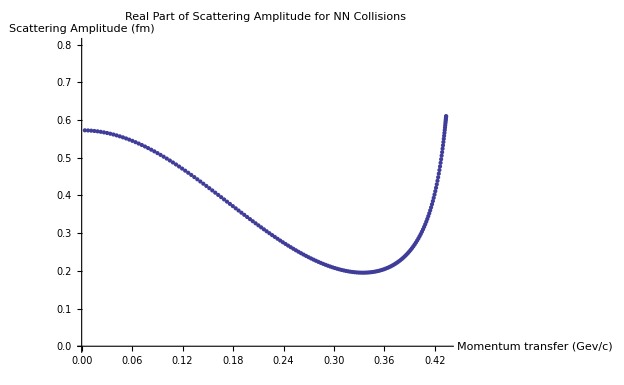

```mathematica
ListPlot[Transpose[{NN100[[All,1]],Re[NN100[[All,2]]]}],PlotLabel->"Real Part of Scattering Amplitude for NN Collisions",AxesLabel->{"Momentum transfer (Gev/c)","Scattering Amplitude (fm)"},PlotRange->{0,0.8}]
```

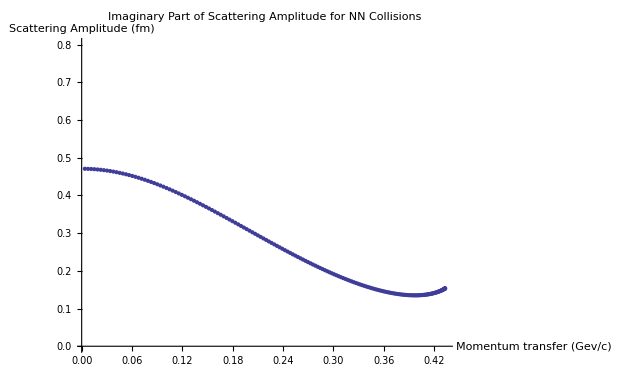

```mathematica
ListPlot[Transpose[{NN100[[All,1]],Im[NN100[[All,2]]]}],PlotLabel->"Imaginary Part of Scattering Amplitude for NN Collisions",AxesLabel->{"Momentum transfer (Gev/c)","Scattering Amplitude (fm)"},PlotRange->{0,0.8}]
```

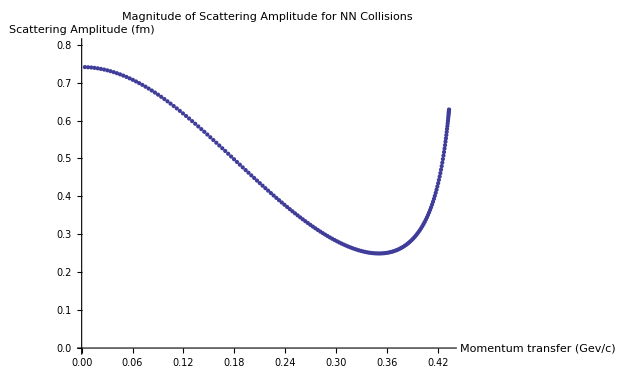

```mathematica
ListPlot[Transpose[{NN100[[All,1]],Abs[NN100[[All,2]]]}],PlotLabel->"Magnitude of Scattering Amplitude for NN Collisions",AxesLabel->{"Momentum transfer (Gev/c)","Scattering Amplitude (fm)"},PlotRange->{0,0.8}]
```

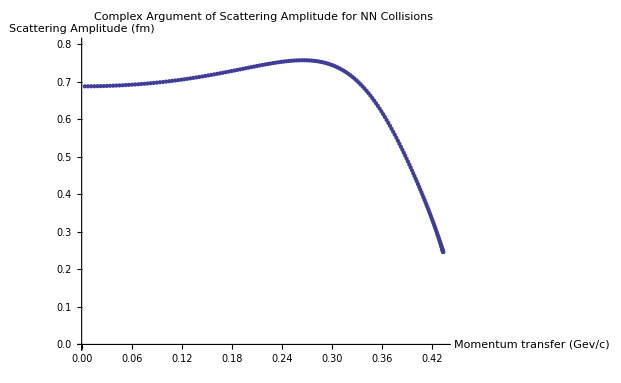

```mathematica
ListPlot[Transpose[{NN100[[All,1]],Arg[NN100[[All,2]]]}],PlotLabel->"Complex Argument of Scattering Amplitude for NN Collisions",AxesLabel->{"Momentum transfer (Gev/c)","Scattering Amplitude (fm)"},PlotRange->{0,0.8}]
```

## Fit data to complex gaussian (see model on next line)

```mathematica
Clear[β,ρ,σ]
model=κ σ (I+ρ)/(4 Pi) Exp[-β q^2];
```

The fit is only performed over the first 50 degrees.

{a→0.740121,βre→12.3977}

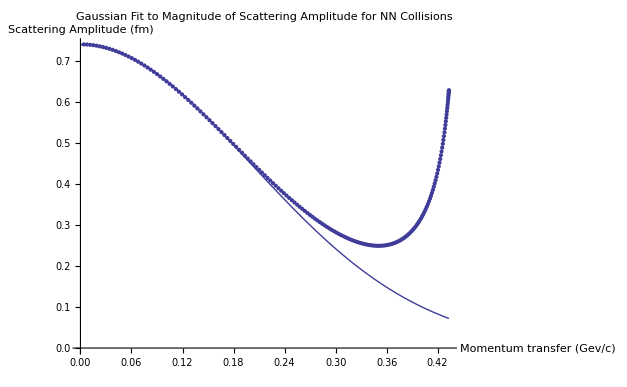

```mathematica
Npts=50;
FindFit[Transpose[{NN100[[1;;Npts,1]],Abs[NN100[[1;;Npts,2]]]}],a Exp[-βre q^2],{a,βre},q]
Show[Plot[a Exp[-βre q^2]/.%,{q,0,2 κ}],ListPlot[Transpose[{NN100[[All,1]],Abs[NN100[[All,2]]]}]],PlotLabel->"Gaussian Fit to Magnitude of Scattering Amplitude for NN Collisions",AxesLabel->{"Momentum transfer (Gev/c)","Scattering Amplitude (fm)"}]
```

{ρ→1.21713,βim→-1.26645}

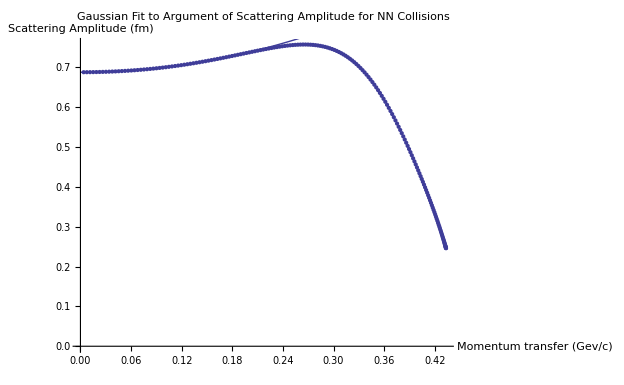

```mathematica
FindFit[Transpose[{NN100[[1;;Npts,1]],Arg[NN100[[1;;Npts,2]]]}],ArcTan[ρ,1]-βim q^2,{ρ,βim},q]
Show[ListPlot[Transpose[{NN100[[All,1]],Arg[NN100[[All,2]]]}]],Plot[ArcTan[ρ,1]-βim q^2/.%,{q,0,2 κ}],PlotLabel->"Gaussian Fit to Argument of Scattering Amplitude for NN Collisions",AxesLabel->{"Momentum transfer (Gev/c)","Scattering Amplitude (fm)"}]
```

```mathematica
NSolve[κ/ℏc σ Sqrt[1+ρ^2]/(4 Pi)==0.7401208259427848&&ρ==1.217127351734708,{σ,ρ}]
```

{{σ→5.37714,ρ→1.21713}}

Fitted parameters:

```mathematica
σ=5.377143967540269;
ρ=1.217127351734708;
β=12.39772991491029-1.2664454506269087 I;
```

## Glauber

```mathematica
σ1=-σ/ℏc^2 (1-I ρ)/(8 Pi β)
Fcm[q_]:=Exp[B*q^2/A]
```

-0.493154+0.489051 ⅈ

```mathematica
F0[q_]:=-2*I*k*Fcm[q]*(B+β)*Sum[Binomial[A,j]/j*(-σ (1-I ρ)/ℏc^2/(8 Pi (B+β)))^j*Exp[-(B+β)*q^2/j],{j,1,A}]*ℏc
```

Glauber approximation  for p-α scattering is below:

```mathematica
40*Pi/(k/ℏc) Im[F0[0]]
```

217.136

```mathematica
ρ0[q_]:=Exp[-B q^2]
```

InterpolatingFunction::dmval: Input value {0.00195861} lies outside the range of data in the interpolating function. Extrapolation will be used.

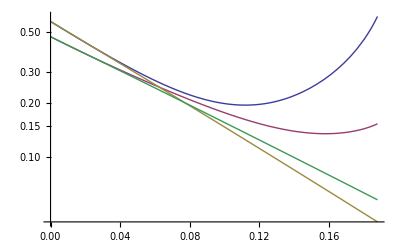

```mathematica
LogPlot[{Re[f[Sqrt[q]]],Im[f[Sqrt[q]]],Re[κ/ℏc σ (I+ρ)/(4 Pi) Exp[-β Sqrt[q]^2]],Im[κ/ℏc σ (I+ρ)/(4 Pi) Exp[-β Sqrt[q]^2]]},{q,0,(2 κ)^2}]
```

InterpolatingFunction::dmval: Input value {0.00195861} lies outside the range of data in the interpolating function. Extrapolation will be used.

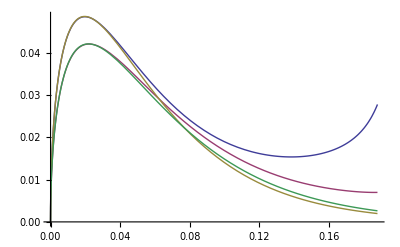

```mathematica
Plot[{Re[Sqrt[q]f[Sqrt[q]] ρ0[Sqrt[q]]],Im[Sqrt[q] f[Sqrt[q]] ρ0[Sqrt[q]]],Re[Sqrt[q] κ/ℏc σ (I+ρ)/(4 Pi) Exp[-β Sqrt[q]^2] ρ0[Sqrt[q]]],Im[Sqrt[q] κ/ℏc σ (I+ρ)/(4 Pi) Exp[-β Sqrt[q]^2] ρ0[Sqrt[q]]]},{q,0,(2 κ)^2}]
```

```mathematica
Γp=Interpolation[Table[{b,1/(I κ) NIntegrate[ρ0[q] BesselJ[0,b q] fp[q]/ℏc q,{q,0,2 κ}]},{b,0,50}]];
Γn=Interpolation[Table[{b,1/(I κ) NIntegrate[ρ0[q] BesselJ[0,b q] fn[q]/ℏc q,{q,0,2 κ}]},{b,0,50}]];
```

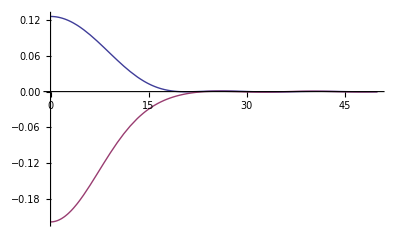

```mathematica
Plot[{Re[Γp[b]],Im[Γp[b]]},{b,0,50},PlotRange->All]
```

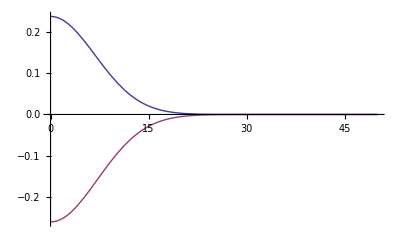

```mathematica
Plot[{Re[σ/ℏc^2 (1-I ρ)/(4B) Exp[-b^2/(4B)/(1+β/B)]/(2 Pi (1+β/B))],Im[σ /ℏc^2(1-I ρ)/(4B) Exp[-b^2/(4B)/(1+β/B)]/(2 Pi (1+β/B))]},{b,0,50},PlotRange->All]
```

```mathematica
Γ[0]
```

0.247052-0.295904 ⅈ

```mathematica
Table[{q,I κ ℏc Exp[q^2B/A] NIntegrate[BesselJ[0,b q](1-(1-Γp[b])^2(1-Γn[b])^2),{b,0,50}]},{q,0,.5,.01}]
```

{{0.,0.226839+0.351632 ⅈ},{0.01,0.226476+0.351325 ⅈ},{0.02,0.225395+0.350409 ⅈ},{0.03,0.223626+0.348896 ⅈ},{0.04,0.221212+0.346807 ⅈ},{0.05,0.218206+0.344168 ⅈ},{0.06,0.214664+0.341011 ⅈ},{0.07,0.210644+0.33737 ⅈ},{0.08,0.206194+0.333281 ⅈ},{0.09,0.201359+0.328782 ⅈ},{0.1,0.196177+0.323912 ⅈ},{0.11,0.190684+0.318711 ⅈ},{0.12,0.184917+0.313223 ⅈ},{0.13,0.178919+0.30749 ⅈ},{0.14,0.172742+0.30156 ⅈ},{0.15,0.166447+0.29548 ⅈ},{0.16,0.160104+0.289301 ⅈ},{0.17,0.153786+0.283069 ⅈ},{0.18,0.147567+0.276834 ⅈ},{0.19,0.141514+0.270636 ⅈ},{0.2,0.13568+0.264516 ⅈ},{0.21,0.130104+0.258505 ⅈ},{0.22,0.124809+0.252633 ⅈ},{0.23,0.119801+0.246921 ⅈ},{0.24,0.115078+0.24139 ⅈ},{0.25,0.110636+0.236057 ⅈ},{0.26,0.106471+0.230939 ⅈ},{0.27,0.102588+0.226055 ⅈ},{0.28,0.099003+0.221421 ⅈ},{0.29,0.0957415+0.217055 ⅈ},{0.3,0.0928341+0.212975 ⅈ},{0.31,0.0903098+0.209192 ⅈ},{0.32,0.0881871+0.205714 ⅈ},{0.33,0.0864654+0.20254 ⅈ},{0.34,0.0851187+0.199662 ⅈ},{0.35,0.0840935+0.197064 ⅈ},{0.36,0.0833107+0.194723 ⅈ},{0.37,0.0826732+0.192616 ⅈ},{0.38,0.0820772+0.190716 ⅈ},{0.39,0.0814258+0.189003 ⅈ},{0.4,0.0806437+0.187466 ⅈ},{0.41,0.0796879+0.186101 ⅈ},{0.42,0.0785558+0.184918 ⅈ},{0.43,0.077286+0.183936 ⅈ},{0.44,0.0759536+0.183183 ⅈ},{0.45,0.0746587+0.182689 ⅈ},{0.46,0.0735121+0.182484 ⅈ},{0.47,0.0726185+0.182592 ⅈ},{0.48,0.0720611+0.183028 ⅈ},{0.49,0.0718904+0.183797 ⅈ},{0.5,0.072118+0.184891 ⅈ}}

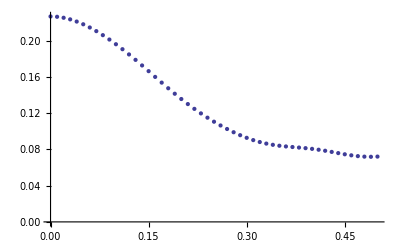

```mathematica
ListPlot[Re[%]]
```

```mathematica
40*Pi/(k/ℏc) Im[F0[0]]
```

217.136

```mathematica
40 Pi/(k/ℏc) Im[I k ℏc NIntegrate[b BesselJ[0,0](1-(1-Γ[b])^A),{b,0,50}]]
```

217.839

```mathematica
40 Pi/(k/ℏc) Im[I k ℏc NIntegrate[b BesselJ[0,0](1-(1-Γp[b])^2(1-Γn[b])^2),{b,0,50}]]
```

219.691